```mathematica
calcpi[Num_]:=Module[{n, count, a, b, r},
n=0;
count = 0.0;
While[n<Num,
a=RandomReal[];
b=RandomReal[];
r=Sqrt[(a-0.5)^2+(b-0.5)^2];
If[r≤0.5, count+=1];
n+=1;
];
N[4.0*count/Num]
]
```

```mathematica
genStatistics[Num_,k_]:=Module[{stats, kk, n, total, kkStats},
stats = {};
kk=1;
While[kk<=k,
stats=Append[stats,{10^kk,Mean[Cases[Range[0,Num],i_/;True:>Abs[Pi - calcpi[10^kk]]]]}];
kk+=1;
];
p1 = ListLogLogPlot[stats];
p2 = LogLogPlot[1/Sqrt[x],{x,1,10^5}];
Return[Show[p1,p2,PlotRange->All]];
]
```

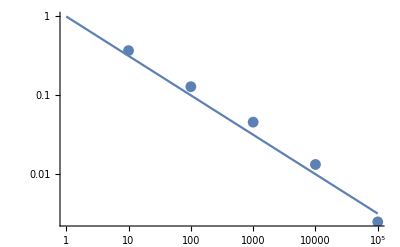

```mathematica
stats =genStatistics[10, 5]
```